# Modeling the Maximum Potential of Rotational Grazing

What I did to change the model:
-switched the energy gain/energy loss values 
-cow energy: gain from eating (+1, +1, +.5, +0), loss from moving (-.5) 
-made the simulation plot size larger and rectangular shaped {(-70, 35), (-70,-35), (70,35), (70,-35)}

In experiment 1, the number of paddocks were tested. 
In experiment 2, the rotation time was tested. 
10 trials for each variable

## Experiment 1: Number of Paddocks

```mathematica
Column[{"Health",Grid[Prepend[(MapThread[Append,{MapThread[Prepend,{healthdata,Range[1,6]}],paddockhealth}]),Join[{"# of paddocks"},Range[1,10],{"average"}]],Frame->All],"Energy",Grid[Prepend[(MapThread[Append,{MapThread[Prepend,{energydata,Range[1,6]}],paddockenergy}]),Join[{"# of paddocks"},Range[1,10],{"average"}]],Frame->All]}]
```

Health
# of paddocks | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | average
1 | 3.37 | -0.12 | 2.25 | 2.85 | 0.79 | 2.27 | 2.83 | -1.8 | 2.03 | 2.02 | 1.649
2 | 2.98 | 3.795 | 2.88 | 3.13 | 3.78 | 1.13 | 0.17 | 0.21 | 2.56 | 0.03 | 2.0665
3 | -0.27 | 3.72 | 1.3 | 1.66 | 0.75 | 2.12 | 2.1 | 0.38 | 3.25 | 2.3 | 1.731
4 | 3.26 | 2.05 | 2.34 | 2.16 | 3.58 | -0.16 | -0.35 | 1.05 | -0.08 | 0.22 | 1.407
5 | 1.11 | -1.09 | -0.03 | 0.59 | 1.12 | 0.59 | 0.68 | -0.54 | 0.94 | -1.13 | 0.224
6 | -1.86 | -0.74 | -1.75 | -0.93 | -0.94 | -1.24 | -1.76 | -0.75 | -0.24 | -0.46 | -1.067
Energy
# of paddocks | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | average
1 | 23.145 | 23.265 | 23.15 | 23.094 | 23.215 | 23.11 | 23.207 | 23.329 | 23.045 | 23.136 | 23.1696
2 | 22.883 | 22.966 | 22.922 | 22.985 | 22.831 | 22.976 | 22.953 | 23.041 | 22.929 | 22.953 | 22.9439
3 | 22.865 | 22.781 | 22.687 | 22.811 | 22.849 | 22.725 | 22.791 | 22.741 | 22.778 | 22.763 | 22.7791
4 | 22.499 | 22.616 | 22.533 | 22.655 | 22.51 | 22.649 | 22.612 | 22.621 | 22.61 | 22.565 | 22.587
5 | 22.441 | 22.458 | 22.357 | 22.468 | 22.217 | 22.385 | 22.32 | 22.454 | 22.319 | 22.41 | 22.3829
6 | 22.254 | 22.205 | 22.196 | 22.15 | 22.375 | 22.21 | 22.304 | 22.212 | 22.219 | 22.268 | 22.2393

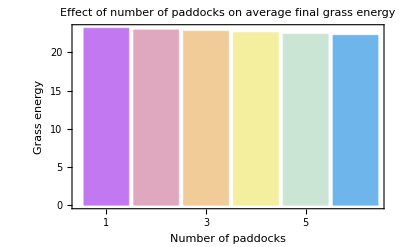

```mathematica
BarChart[paddockenergy,PlotLabel->"Effect of number of paddocks on average final grass energy",ChartLabels->Range[1,6],ChartStyle->"Pastel",Frame->True,FrameLabel->{{"Grass energy",""},{"Number of paddocks",""}}]
```

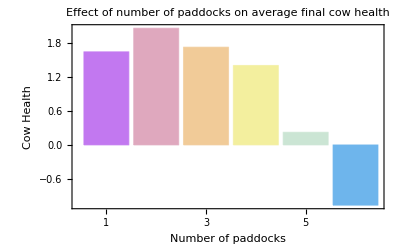

```mathematica
BarChart[paddockhealth,PlotLabel->"Effect of number of paddocks on average final cow health",ChartLabels->Range[1,6],ChartStyle->"Pastel",Frame->True,FrameLabel->{{"Cow Health",""},{"Number of paddocks",""}}]
```

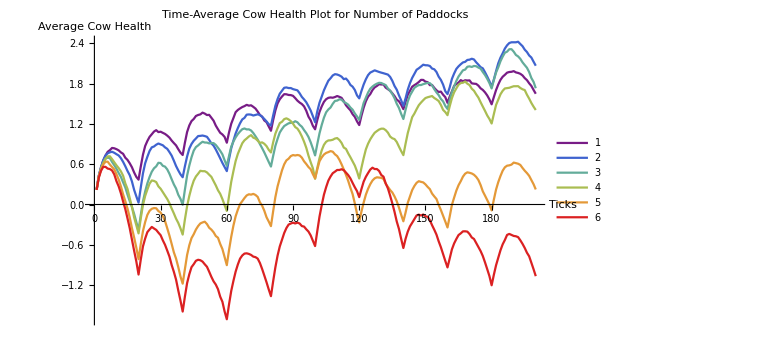

```mathematica
healthplot=ListLinePlot[Map[meanall[#]&,healthticks],AxesLabel->{"Ticks","Average Cow Health"},PlotLegends->{Range[1,6]},ImageSize->Large,PlotStyle->"Rainbow",PlotLabel->"Time-Average Cow Health Plot for Number of Paddocks"]
```

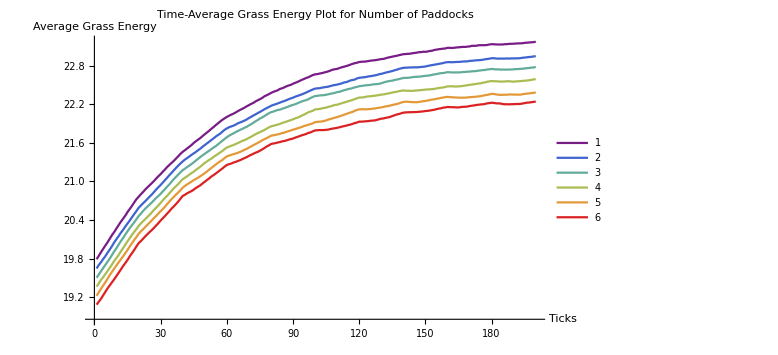

```mathematica
energyplot=ListLinePlot[Map[meanall[#]&,energyticks],PlotRange->All,AxesLabel->{"Ticks","Average Grass Energy"},ImageSize->Large,PlotStyle->"Rainbow",PlotLegends->{Range[1,6]},PlotLabel->"Time-Average Grass Energy Plot for Number of Paddocks"]
```

## Experiment 2: Rotation Time

```mathematica
Column[{"Health",Grid[Prepend[(MapThread[Append,{MapThread[Prepend,{healthdata2,Range[10,60,10]}],timehealth}]),Join[{"rotation time"},Range[1,10],{"average"}]],Frame->All],"Energy",Grid[Prepend[(MapThread[Append,{MapThread[Prepend,{energydata2,Range[10,60,10]}],timeenergy}]),Join[{"rotation time"},Range[1,10],{"average"}]],Frame->All]}]
```

Health
rotation time | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | average
10 | 603.5 | 520. | 501.5 | 481.5 | 450. | 530. | 451. | 498. | 507.5 | 502. | 504.5
20 | -22. | 13. | 39.5 | 92.5 | 20. | 20.5 | 15. | 100.5 | 67. | 64.5 | 41.05
30 | -309.5 | -265.5 | -134.5 | -278.5 | -222.5 | -287. | -254. | -253. | -250. | -195.5 | -245.
40 | -591. | -461.5 | -446.5 | -716.5 | -535. | -714.5 | -483.5 | -460.5 | -602. | -560.5 | -557.15
50 | -623. | -698.5 | -628.5 | -772.5 | -653.5 | -553.5 | -591.5 | -780. | -574.5 | -427.5 | -630.3
60 | -642.5 | -861. | -603. | -548. | -557. | -707. | -607.5 | -609. | -628. | -735. | -649.8
Energy
rotation time | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | average
10 | 221.88 | 221.96 | 222.34 | 221.33 | 221.52 | 221.58 | 221.49 | 223.3 | 222.41 | 221.23 | 221.904
20 | 224.77 | 224.09 | 223.42 | 223.87 | 223.87 | 223.88 | 223.39 | 223.79 | 223.54 | 223.66 | 223.828
30 | 225.07 | 226.09 | 224.72 | 224.83 | 226.09 | 226.27 | 224.43 | 224.98 | 226.11 | 225.58 | 225.417
40 | 227.29 | 225.6 | 226.1 | 227.63 | 225.78 | 227.19 | 227.35 | 226.96 | 227.2 | 227.08 | 226.818
50 | 226.88 | 228.28 | 227.52 | 229.08 | 227.1 | 227.93 | 227.2 | 228.53 | 227.21 | 226.15 | 227.588
60 | 226.6 | 228.97 | 227.26 | 227.09 | 226.9 | 227.75 | 227.87 | 227.78 | 228.5 | 227.3 | 227.602

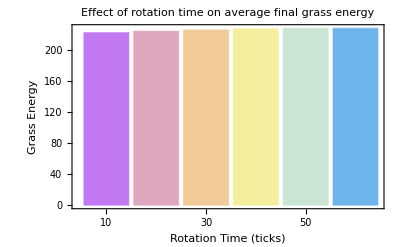

```mathematica
BarChart[timeenergy,PlotLabel->"Effect of rotation time on average final grass energy",ChartLabels->Range[10,60,10],ChartStyle->"Pastel",Frame->True,FrameLabel->{"Rotation Time (ticks)","Grass Energy"}]
```

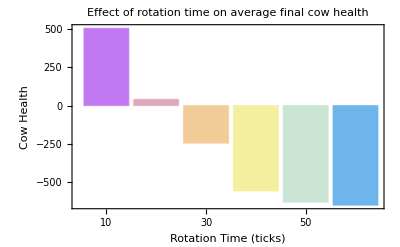

```mathematica
BarChart[timehealth,PlotLabel->"Effect of rotation time on average final cow health",ChartLabels->Range[10,60,10],ChartStyle->"Pastel",Frame->True,FrameLabel->{"Rotation Time (ticks)","Cow Health"}]
```

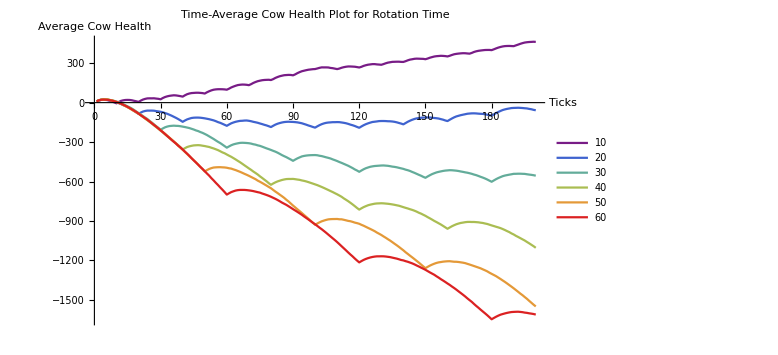

```mathematica
healthplot2=ListLinePlot[Map[meanall[#]&,healthticks2],AxesLabel->{"Ticks","Average Cow Health"},PlotLegends->{Range[10,60,10]},ImageSize->Large,PlotStyle->"Rainbow",PlotLabel->"Time-Average Cow Health Plot for Rotation Time"]
```

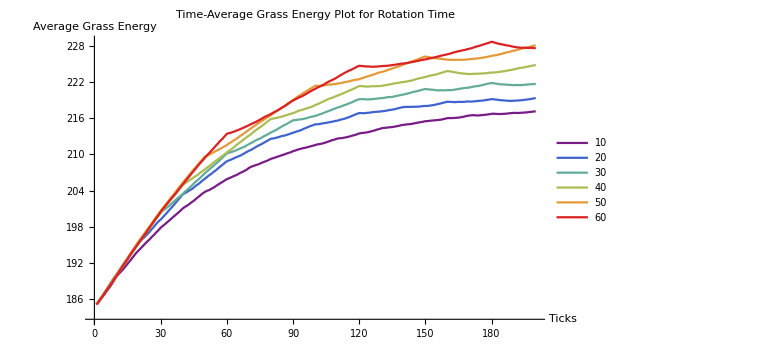

```mathematica
energyplot2=ListLinePlot[Map[meanall[#]&,energyticks2],AxesLabel->{"Ticks","Average Grass Energy"},PlotLegends->{Range[10,60,10]},ImageSize->Large,PlotStyle->"Rainbow",PlotLabel->"Time-Average Grass Energy Plot for Rotation Time"]
```